```mathematica
fx[x_,y_,t_]:=(2-1.2*y)*x
fy[x_,y_,t_]:=(-1+0.9*x)*y
```

```mathematica
(*Euler*)
Euler[t_,t0_,x0_,y0_,n_]:=Module[{i,xx,dx,yy,dy,tt=t0,dt},
dt=(t-t0)/n;
xx=x0;
yy=y0;
For[i=1,i≤ n, i++,
dx=fx[xx,yy,tt]*dt;
dy=fy[xx,yy,tt]*dt;
tt=t0+i*dt;
xx=xx+dx;
yy=yy+dy
];
{xx,yy}//N
]
Euler[5, 0, 1, 0.5, 400]
```

{0.874093,0.46438}

```mathematica
(* NDSolve *)
s = NDSolve[{x'[t]==fx[x[t], y[t], t],
y'[t]==fy[x[t],y[t],t], x[0]==1, y[0]==0.5}, {x,y}, {t,0,15}]
```

{{x→InterpolatingFunction[{{0., 15.}}, <>],y→InterpolatingFunction[{{0., 15.}}, <>]}}

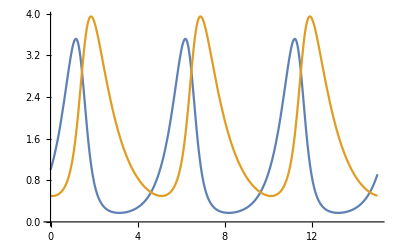

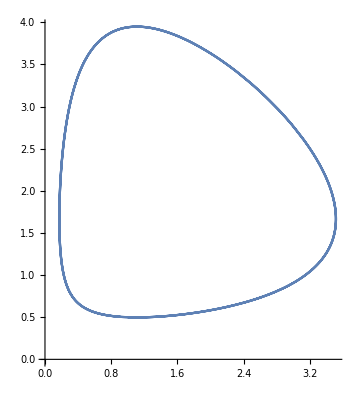

```mathematica
Plot[Evaluate[{x[t], y[t]}/.s], {t,0,15}]
ParametricPlot[Evaluate[{x[t], y[t]}/.s], {t,0,15}]
```